```mathematica
$Assumptions Element[x, PositiveIntegers]
$Assumptions Element[t, PositiveIntegers]
$Assumptions Element[N, PositiveIntegers]
P1[i_,t_] := 1/N +  2/N *Sum[
Cos[(i-1/2)*   Pi * k / N ] * Cos[  Pi * k / N/2 ] ^ (2*t +1),
{k, 1, N-1}
]
PN[i_,t_] := 1/N +  2/N *Sum[
Cos[(N-1/2)(k π)/N]*Cos[(i-1/2)*   Pi * k / N ] *  Cos[  Pi * k / N/2 ] ^ (2*t),
{k, 1, N-1}
]
```

True (x∈ℤ&&x>0)

True (t∈ℤ&&t>0)

True (N∈ℤ&&N>0)

The thing we care ∑P_1(i,t)P_N(i,t) = ∑P(i,t)P(N-i,t)

```mathematica
Sum[P1[i,t]*PN[i,t], {i,1, N}]
```

```mathematica
∑_(i=1)^N (1/N+(2 ∑_(k=1)^(-1+N) Cos[(k π)/(2 N)]^(1+2 t) Cos[((-1/2+i) k π)/N])/N) (1/N+(2 ∑_(k=1)^(-1+N) Cos[(k π)/(2 N)]^(2 t) Cos[((-1/2+i) k π)/N] Cos[(k (-1/2+N) π)/N])/N)
```

$Aborted

```mathematica
fN[N_, i_, t_] := 1/N+(2 ∑_(k=1)^(-1+N) Cos[(N-1/2)(k π)/N]  Cos[(k π)/(2 N)]^(2 t) Cos[((-1/2+i) k π)/N])/N
fN[10,10,1] // N
f1[N_, i_, t_] := 1/N+(2 ∑_(k=1)^(-1+N) Cos[(k π)/(2 N)]^(1+2 t) Cos[((-1/2+i) k π)/N])/N
f1[10,1,0] // N
```

0.75

1.

```mathematica
testF[N_, t_]:= 1/N + 4/N^2 Sum[
Sum[
Cos[(i-1/2)*   Pi * j / N ] * Cos[  Pi * j / N/2 ] ^ (2*t +1),
{j, 1, N-1}
]*Sum[
Cos[(N-1/2)(k π)/N]*Cos[(i-1/2)*   Pi * k / N ] *  Cos[  Pi * k / N/2 ] ^ (2*t),
{k, 1, N-1}
],
{i, 1, N}
]
```

```mathematica
Sum[f1[10,i, 6]* fN[10,i,6], {i,1,10}] // N
testF[10, 6] // N
```

0.000154972

0.000154972

```mathematica
0.4189453125000001 fN[10.,1.,6.]+0.31420898437500006 fN[10,2.,6.]+0.174560546875 fN[10.,3.,6.]+0.06982421874999999 fN[10.,4.,6.]+0.019042968749999986 fN[10.,5.,6.]+0.003173828125000014 fN[10.,6.,6.]+0.00024414062500004163 fN[10.,7.,6.] // N
```

0.000154972

```mathematica
fN[10.,1.,6.] //N
```

```mathematica
TestF2[N_, t_]:= 1/N + 4/N^2 Sum[
Cos[(k π)/(2 N)]^(1+2 t) Cos[((-1/2+i) k π)/N] Cos[(j π)/(2 N)]^(2 t) Cos[((-1/2+i) j π)/N] Cos[(j (-1/2+N) π)/N],
{i,1,N},{j,1,N-1}, {k,1,N-1}
]
```

-1.80411×10^-16

```mathematica
N[testF2[10, 6]]
```

testF2[10.,6.]

```mathematica
1/10+1/10^2 Sum[
Cos[(j π)/(2 N)]^(1+2 t) Cos[((-1/2+i) j π)/N] Cos[(k π)/(2 N)]^(2 t) Cos[((-1/2+i) k π)/N] Cos[(k (-1/2+N) π)/N],
{i,1,10},{j,1,10-1}, {k,1,10-1}
] //N
```

0.0750387

```mathematica
Cos[(i-1/2)*   Pi * j / N ] * Cos[  Pi * j / N/2 ] ^ (2*t +1)*Cos[(N-1/2)(k π)/N]*Cos[(i-1/2)*   Pi * k / N ] *  Cos[  Pi * k / N/2 ] ^ (2*t)
```

```mathematica
Cos[(j π)/(2 N)]^(1+2 t) Cos[((-1/2+i) j π)/N] Cos[(k π)/(2 N)]^(2 t) Cos[((-1/2+i) k π)/N] Cos[(k (-1/2+N) π)/N]

f[N_, t_] := 1/N + 2/N * Sum[
Cos[k*Pi/2/N]^(1+4*t)cos((k*(N-1/2)*pi)/N),
{k,1,N-1}
]
```

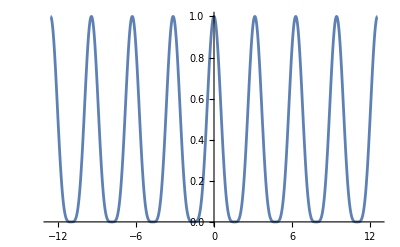

```mathematica
Plot[Cos[x]^4, {x, -4Pi, 4Pi}]
```

```mathematica
Cos[(Pi k (N-1/2))/N]Cos[(Pi k)/(2 N)] // TrigReduce
```

1/2 (Cos[(k π)/(2 N)-(k (-1/2+N) π)/N]+Cos[(k π)/(2 N)+(k (-1/2+N) π)/N])

```mathematica
Cos[(k π)/(2 N)-(k (-1/2+N) π)/N] // Simplify // TeXForm
```

\cos \left(\frac{\pi  k (N-1)}{N}\right)

```mathematica
Cos[(k π)/(2 N)+(k (-1/2+N) π)/N] // Simplify// TeXForm
```

\cos (\pi  k)

```mathematica
Sum[Cos[Pi k]* Cos[(Pi k)/(2N)]^(4t), {k , 1 , N-1}, Assumptions->Element[N, PositiveIntegers]]
```

```mathematica
Sum[(-1)^k * Cos[(k π)/(2 N)]^(4 t),{k,1,-1+N},Assumptions->N∈Integers&&N>0]
```

Sum[(-1)^k Cos[(k π)/(2 N)]^(4 t),{k,1,-1+N},Assumptions→N∈ℤ&&N>0]

```mathematica
Sum[Cos[(k Pi)/(2 N) ]^t, {k, 1, N-1}]
```

∑_(k=1)^(-1+N) Cos[(k π)/(2 N)]^t

```mathematica
Cos[(Pi k (N-1))/N] // TrigExpand
```

Cos[(k (-1+N) π)/N]

```mathematica
TrigExpand[Cos[A+B]]
```

Cos[A] Cos[B]-Sin[A] Sin[B]

```mathematica
(Cos[(2Pi m)/N]+1)Cos[(Pi m)/N]^(4t) - (Cos[(Pi (2m-1))/N]+1)Cos[(Pi (2m-1))/(2N)]^(4t) // Simplify
```

2 (Cos[(m π)/N]^(2+4 t)-Cos[((-1+2 m) π)/(2 N)]^(2+4 t))

```mathematica
Cos[-π/(2 N) + mπ/N] // TrigExpand
```

Cos[mπ/N] Cos[π/(2 N)]+Sin[mπ/N] Sin[π/(2 N)]

```mathematica
Cos[(2Pi m)/N] Cos[(Pi m)/N]^(4t) - Cos[(Pi (2m-1))/N] Cos[(Pi (2m-1))/(2N)]^(4t) + Cos[(Pi m)/N]^(4t) -Cos[(Pi (2m-1))/(2N)]^(4t)// Simplify
```

2 (Cos[(m π)/N]^(2+4 t)-Cos[((-1+2 m) π)/(2 N)]^(2+4 t))

```mathematica
Cos[(Pi(N-1))/(2N)] // Simplify
```

Sin[π/(2 N)]

```mathematica
(Cos[(Pi(N-1))/N]+1)Cos[(Pi(N-1))/(2N)]^(4t) // Simplify
```

2 Sin[π/(2 N)]^(2+4 t)

```mathematica
Integrate[Cos[k]^(2p), {k,0, Pi/2 - a}, Assumptions->(Element[p, PositiveIntegers]&& 0<a<Pi/2)]
```

1/2 (-Beta[Sin[a]^2,1/2+p,1/2]+(√π Gamma[1/2+p])/Gamma[1+p])

```mathematica
Integrate[Cos[k]^(2p), {k,a, Pi/2 }, Assumptions->(Element[p, PositiveIntegers]&& 0<a<Pi/2)]
```

1/2 Beta[Cos[a]^2,1/2+p,1/2]

```mathematica
Fup[p_, N_] = 
F[p_, N_]
Fdown[p_, N_]
Beta[1,2]
```

Rule::rhs: 模式 p_ 出现在规则 Fup[p_,N_]→F[p_,N_] 的右边.

Rule::rhs: 模式 N_ 出现在规则 Fup[p_,N_]→F[p_,N_] 的右边.

F[p_,N_]

Fdown[p_,N_]

1/2

```mathematica
Beta[1,2,1/3]
```

9/4

```mathematica
Beta[1,2,1/4]
```

16/5

```mathematica
Beta[0.5, 1,2]
```

0.375

```mathematica
Beta[0.5, 2,4]
```

0.040625

```mathematica
1/π Beta
```

20

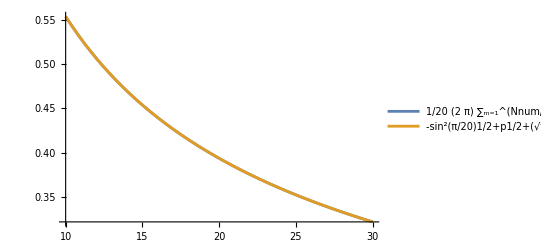

-Graphics-

```mathematica
Nnum = 20
Plot[{
(2Pi)/Nnum*Sum[Cos[(m Pi)/Nnum]^(2p),{m,1,Nnum/2}]+ Pi/Nnum,
-Beta[Sin[Pi/Nnum]^2,1/2+p,1/2]+(√π Gamma[1/2+p])/Gamma[1+p]
}, {p, 10,30}, PlotLegends->"Expressions"]

Plot[{

}, {p, 10,30}, PlotLegends->"Expressions"]
```

```mathematica
func[w_]:= -1/Pi Beta[Sin[Pi/N]^2,1/2+2/w+1,1/2]+Gamma[1/2+2/w+1]/(√π Gamma[1+2/w+1]) - 1/Pi Beta[Cos[Pi/N]^2,1/2+2/w+1,1/2]
```

```mathematica
Series[func[w], {w,0, 2}, Assumptions->(Element[N, PositiveIntegers]&& w>0)]
```

-Beta[Cos[π/N]^2,3/2+2/w,1/2]/π-Beta[Sin[π/N]^2,3/2+2/w,1/2]/π+((√w)/(√(2 π))-(5 w^(3/2))/(16 √(2 π))+O[w]^(5/2))

```mathematica
Series[-Beta[Cos[π/N]^2,3/2+2/w,1/2]/π-Beta[Sin[π/N]^2,3/2+2/w,1/2]/π, {w,0,1},  Assumptions->(Element[N, PositiveIntegers]&& w>0)]
```

-Beta[Cos[π/N]^2,3/2+2/w,1/2]/π-Beta[Sin[π/N]^2,3/2+2/w,1/2]/π